# 1. Wczytanie plików

```mathematica
path="/home/michaszko/Documents/Neutrina/Opus";
type="LFG";
scalingFactor=10^40;
mecDim=24;

matVanilla=Import[path<>"/Data/matrix_"<>type<>".dat","Table"];
mecVanillaMatrix=Import[path<>"/Data/cros_mec_nuwro_"<>type<>".dat"];
totalVanillaMatrix=Import[path<>"/Data/cros_total_nuwro_"<>type<>".dat"];
danielVanillaMatrix=Import[path<>"/Data/cros_total_daniel.dat"];
errorVanillaMatrix=Import[path<>"/Data/cros_error_daniel.dat"];

mecVanilla=Flatten[Transpose[mecVanillaMatrix]]*scalingFactor;
totalVanilla=Flatten[Transpose[totalVanillaMatrix]]*scalingFactor;
danielVanilla=Flatten[Transpose[danielVanillaMatrix]]*scalingFactor;
errorVanilla=Flatten[Transpose[errorVanillaMatrix]]*scalingFactor;

covInvVanilla=Import[path<>"/Data/daniel_covariance_inv.dat"];
covNonVanilla=Import[path<>"/Data/daniel_covariance_vanilla.dat"];
covVanilla=PseudoInverse[covNonVanilla]*1/scalingFactor^2;

Subscript[Δp, T]={75,75,100,75,75,75,75,150,150,150,250,250,1000};
Subscript[Δp, L]={500,500,500,500,500,500,500,1000,2000,2000,5000,5000};
widthVanilla=Flatten[KroneckerProduct[Subscript[Δp, T],Subscript[Δp, L]]];

eventsNumber=Total[matVanilla,2];
crossSection=1.19683*10^-39;

(**********************************************)

pos=Position[Thread[danielVanilla==0],True];
width=Delete[widthVanilla,pos];
mec=Delete[mecVanilla,pos]*10^40;
daniel=Delete[danielVanilla,pos]*10^40;
total=Delete[totalVanilla,pos]*10^40;
error=Delete[errorVanilla,pos]*10^40;
cov=Delete[Transpose[Delete[covVanilla,pos]],pos]*10^-80;

roz=daniel-total+mec;
roz=roz/.(y_/;y<0)->0;

rozVanilla=danielVanilla-totalVanilla+mecVanilla;
rozVanilla=rozVanilla/.(y_/;y<0)->0;

errorVanillaError = errorVanilla/.(y_/;y==0)->1;

MatrixPlot[matVanilla];
(*Print["Rząd macierzy nie zmienionej to ",MatrixRank[matVanilla], " a jej wymiary to ",Dimensions[matVanilla]];*)

removed=Flatten[Table[mecDim*i-j,{i,1,mecDim},{j,mecDim-i,0,-1}]];
mat=Delete[matVanilla,pos];
mat=Transpose[mat];
mat=Part[mat,removed];
mat=Transpose[mat];

MatrixPlot[mat];
(*Print["Rząd macierzy zmienionej to ",MatrixRank[mat], " a jej wymiary to ",Dimensions[mat]]*)
{ equations,variables}=Dimensions[mat];

(***************************************************)

mat=(mat*10^40)/5000000*crossSection*1000000/width*12/13;
matVanilla=matVanilla/5000000*crossSection*1000000/widthVanilla*12/13*scalingFactor;

(**************************************************)

BarChart[Partition[Plus@@Transpose[matVanilla],12][[#]],GridLines->Automatic,BarSpacing->None,ImageSize->Large,PlotLabel->(#-1)]&/@Range[13];
MatrixPlot[Partition[Plus@@matVanilla,mecDim],DataReversed->True,PlotLegends->Automatic];
Plus@@Transpose[matVanilla]-mecVanilla//ListPlot;
```

# 2. Test

## χ^2 bez kowariancji

```mathematica
newVanilla=matVanilla.ConstantArray[1,mecDim^2];
errorVanillaError = errorVanilla/.(y_/;y==0)->1;


x=(danielVanilla-totalVanilla+mecVanilla-newVanilla)^2/errorVanillaError^2;
Plus@@Transpose[Partition[x,12]];
MatrixForm[Partition[x,12]];
MatrixPlot[Partition[x,12],PlotLegends->Automatic];
χ=Plus@@x;
```

## χ^2 z kowariancją

```mathematica
newVanilla=matVanilla.ConstantArray[1,mecDim^2];
(newVanilla-Plus@@Transpose[matVanilla])*10^40;
(newVanilla-mecVanilla)*10^40;
(danielVanilla-totalVanilla+mecVanilla-newVanilla).covVanilla.(danielVanilla-totalVanilla+mecVanilla-newVanilla);
```

## Dodatki do χ^2 z kowariancją

```mathematica
Partition[(danielVanilla-totalVanilla+mecVanilla-newVanilla)*covVanilla.(danielVanilla-totalVanilla+mecVanilla-newVanilla),12];
MatrixPlot[%,PlotLegends->Automatic];
MatrixForm@%%;
```

## Test macierzy kowaricanji

```mathematica
MatrixPlot[Partition[(Diagonal[covNonVanilla]/(1/errorVanillaError^2))/.(y_/;y>100 || y<-100)->1,12],PlotLegends->Automatic];
Histogram[(Diagonal[covNonVanilla]/(1/errorVanillaError^2))/.(y_/;y>100 || y<-100)->0];
Clear[chi2cov]
covNonVanilla.covVanilla//Chop//MatrixForm;
(Diagonal[covNonVanilla]-errorVanillaError^2)*10^80;
```

# 3. Rozwiązanie

```mathematica
V=Table[Subscript[v, i,j],{i,1,mecDim},{j,1,mecDim}]//Flatten ;
V1=Table[Subscript[v, i,j],{i,1,mecDim},{j,i,mecDim}]//Flatten;
V2=Table[Subscript[v, i,j],{i,2,mecDim},{j,1,i-1}]//Flatten;
V3=V/.Thread[V2->0.3];

chi2[x_]:=Plus@@((rozVanilla-matVanilla.x)^2/errorVanillaError^2)

chi2cov[x_]:=Module[{u},
u=(rozVanilla-matVanilla.x);
u.covVanilla.u]

plotMec[x_]:=MatrixPlot[
Partition[x,mecDim],
PlotLegends->Automatic,
DataReversed->True,
PlotLabel->{"χ^2 ="<> ToString[chi2[x]]}]


condition=Module[{a,p},
p=0.5;
a=Join[
Thread[V1≥ 0],
(*Thread[Subscript[V, 2]==1],*)
Flatten[Table[Abs[(Subscript[v, i,j]-Subscript[v, i,j-1])/(Subscript[v, i,j]+Subscript[v, i,j-1])]<p,{i,1,mecDim},{j,2,mecDim}]],
Flatten[Table[Abs[(Subscript[v, i,j]-Subscript[v, i,j+1])/(Subscript[v, i,j]+Subscript[v, i,j+1])]<p,{i,1,mecDim},{j,1,mecDim-1}]],
Flatten[Table[Abs[(Subscript[v, i,j]-Subscript[v, i-1,j])/(Subscript[v, i,j]+Subscript[v, i-1,j])]<p,{i,2,mecDim},{j,1,mecDim}]],
Flatten[Table[Abs[(Subscript[v, i,j]-Subscript[v, i+1,j])/(Subscript[v, i,j]+Subscript[v, i+1,j])]<p,{i,1,mecDim-1},{j,1,mecDim}]]];
And@@DeleteDuplicates[a/.Thread[V2->1]]];

minChi2[fun_,iter_:Automatic,acura_:Automatic,prec_:Automatic]:=NMinimize[
{fun[V3],condition},
V1,
MaxIterations->iter,
AccuracyGoal->acura,
PrecisionGoal->prec,
StepMonitor:>(
Export[path<>"/chi2Values/"<>ToString[fun]<>"_"<>ToString[Round[chi2[V3]]]<>".dat",Partition[V3,mecDim]];Print[plotMec[V3]];
ClearSystemCache[])];
```

```mathematica
ClearSystemCache[]
```

## χ^2 bez kowariancji

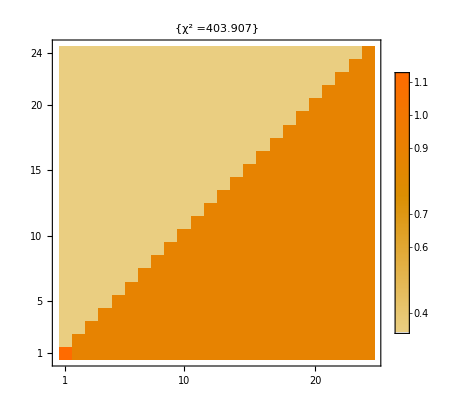

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

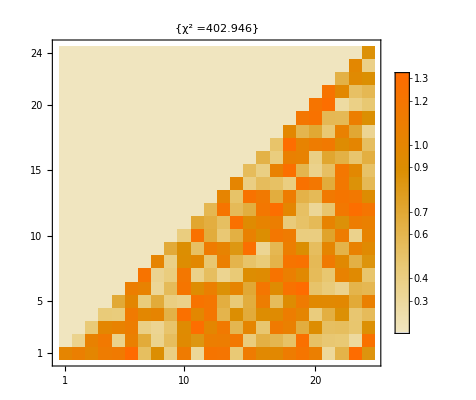

-Graphics-

-Graphics-

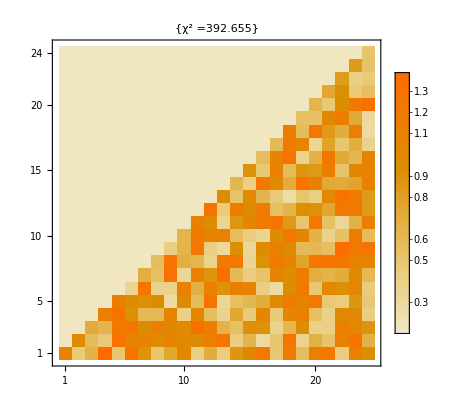

-Graphics-

-Graphics-

-Graphics-

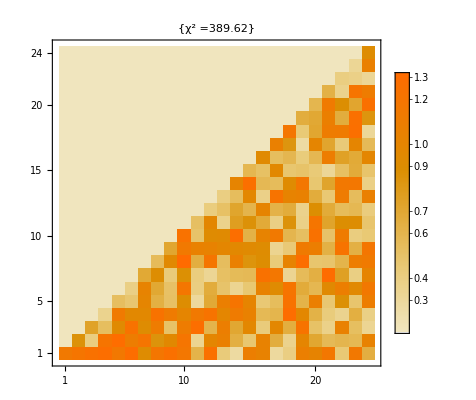

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

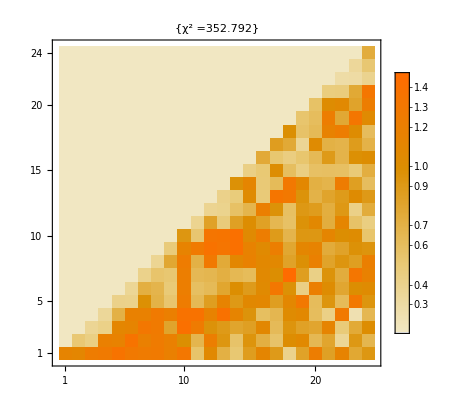

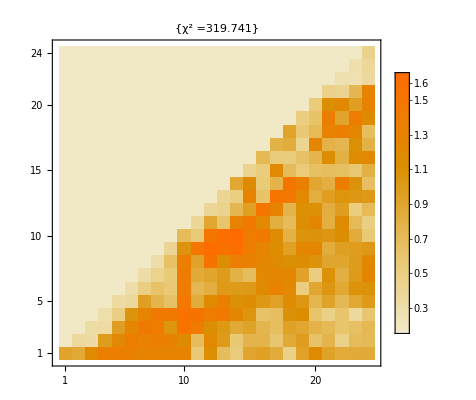

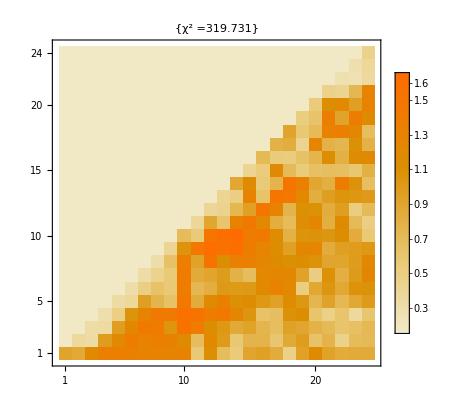

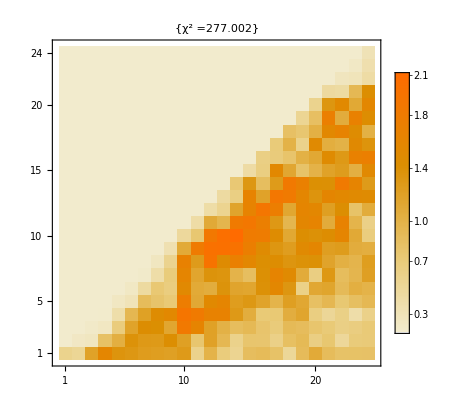

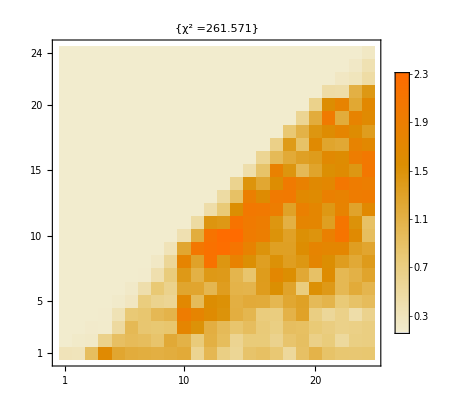

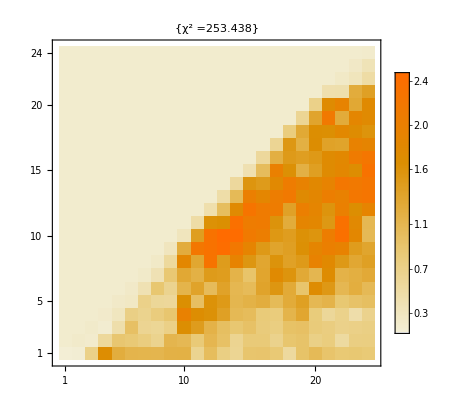

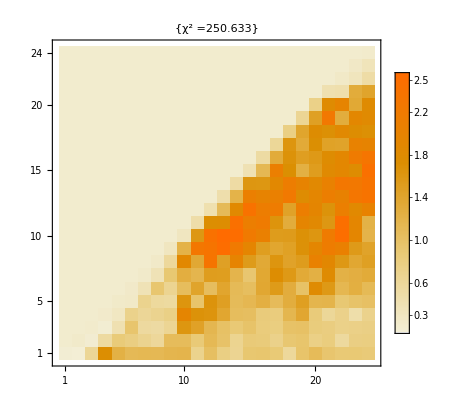

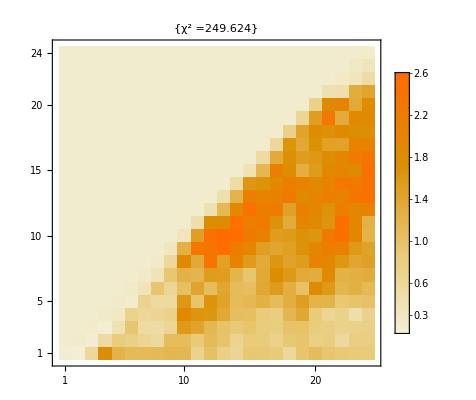

-Graphics-

-Graphics-

-Graphics-

«385 more identical outputs»

```mathematica
{chi2Value,chi2Solution}=minChi2[chi2];
```

## χ^2 z kowariancją

```mathematica
{chi2CovValue,chi2CovSolution}=minChi2[chi2cov,3]
```

-Graphics-

-Graphics-

-Graphics-

«2 more identical outputs»

-Graphics-.

# 4. χ^2

```mathematica
(*chi2cov[x_]:=
((*old=(λ/.(Thread[Variables[λ]->x]))/.(y_/;y<0)->0;*)
old=(((Vall/.Flatten@ssol)/.Thread[Variables[λ]->x])/.Subscript[v, _]->1)/.(y_/;y<0(*||y>10^0*))->0;
new=matVanilla.old;
(*(daniel-total+mec-new).cov.(daniel-total+mec-new)*)
(danielVanilla-totalVanilla+mecVanilla-new).covVanilla.(danielVanilla-totalVanilla+mecVanilla-new))

chi2Values={};
randList={};
Do[
temp=RandomReal[{0,10},Length[Variables[λ]]];
(*temp=ConstantArray[RandomReal[{0,10}],Length[Variables[λ]]];*)
AppendTo[randList,temp];
AppendTo[chi2Values,chi2cov[temp]],
{n,0,1000}]
ListPlot[{chi2Values,Table[Mean[chi2Values],{i,0,Length[chi2Values]}]}]
minList=randList[[Flatten@Position[chi2Values,Min[chi2Values]]]];
minValues=Min[chi2Values]

final=(((Vall/.Flatten@ssol)/.Thread[Variables[λ]->Flatten@minList])/.Subscript[v, _]->1)/.(y_/;y<0(*||y>10^0*))->0
final//Length
MatrixForm[Partition[final,Sqrt[Length[final]]]]
MatrixPlot[Partition[Log10[final],Sqrt[Length[final]]],DataReversed->True,PlotLegends->Automatic]
Export["good.png",%,ImageSize->3000]*)
```

# 4a. χ^2

```mathematica
(*chi2Values={};
randList={};
Do[
temp=RandomReal[{0,2},Length[Variables[λ]]];
(*temp=ConstantArray[RandomReal[{0,10}],Length[Variables[λ]]];*)
AppendTo[randList,temp];
AppendTo[chi2Values,χ[temp]],
{n,0,100}]
ListPlot[{chi2Values,Table[Mean[chi2Values],{i,0,Length[chi2Values]}]}];
minList=randList[[Flatten@Position[chi2Values,Min[chi2Values]]]];
minValues=Min[chi2Values]

final=(((Vall/.Flatten@ssol)/.Thread[Variables[λ]->Flatten@minList])/.Subscript[v, _]->1)(*/.(y_/;y<0(*||y>10^0*))->0*);
MatrixForm[Partition[final,Sqrt[Length[final]]]]
MatrixPlot[Partition[final,Sqrt[Length[final]]],DataReversed->True,PlotLegends->Automatic]
Export["good.png",%,ImageSize->3000]*)
```

# 5. Norma

```mathematica
(*normCheck[x_]:=
(x0=(λ/.Thread[Variables[λ]->x])/.(y_/;y<0(*||y>10^0*))->0;
Norm[mat.x0])

normList={};
normrandList={};
Do[
temp=RandomReal[{0,5},Length[Variables[λ]]];
(*temp=ConstantArray[RandomReal[{0,10}],Length[Variables[λ]]];*)
AppendTo[normrandList,temp];
AppendTo[normList,normCheck[temp]],
{n,0,100}]
ListPlot[{normList,Table[Mean[normList],{i,0,Length[normList]}]}]
normrandList[[Flatten@Position[normList,Min[normList]]]]
Min[normList]*)
```

# 6. LinearSolve

```mathematica
(*Subscript[λ, 1]=LeastSquares[mat,roz]
mat;

old=Subscript[λ, 1]/.y_/;y<0->0
new=mat.old;
(*MatrixPlot[Partition[new,11]]*)
chi2=(daniel-total+mec-new).cov.(daniel-total+mec-new)
(*lolchi2=new.cov.new*)


final=(((Vall/.Thread[V->Subscript[λ, 1]]))/.Subscript[v, _]->0)/.(y_/;y<0(*||y>10^0*))->0;
MatrixForm[Partition[final,Sqrt[Length[final]]]]
MatrixPlot[Partition[final,Sqrt[Length[final]]],DataReversed->True,PlotLegends->Automatic]
Export["matrix.png",%,ImageSize->1000]*)
```

# 7. Minimizing solution’s vector

```mathematica
(*Subscript[λ, 2]=ArgMin[Join[V.V/.ssol,Thread[V>0]],V];*)
(*Subscript[λ, 2]=ArgMin[V.V/.ssol,V];*)
```

```mathematica
(*chi2:=(
old=Subscript[λ, 2]/.(y_/;y<0(*||y>10^0*))->0;
new=mat.old;
(*ListPlot[Log@new]*)
(daniel-total+mec-new).cov.(daniel-total+mec-new))
chi2

final=(((Vall/.Thread[V->Subscript[λ, 2]]))/.Subscript[v, _]->0)/.(y_/;y<0(*||y>10^0*))->0;
MatrixForm[Partition[final,Sqrt[Length[final]]]]
MatrixPlot[Partition[final,Sqrt[Length[final]]],DataReversed->True,PlotLegends->Automatic]*)
```

```mathematica
(*chi2cov[x_]:=
(old=(λ/.(Thread[Variables[λ]->x]))/.(y_/;y<0)->0;
new=mat.old;
(daniel-total+mec-new).cov.(daniel-total+mec-new))

chi2Values={};
randList={};
Do[
temp=RandomReal[{0,10},Length[Variables[λ]]];
(*temp=ConstantArray[RandomReal[{0,10}],Length[Variables[λ]]];*)
AppendTo[randList,temp];
AppendTo[chi2Values,chi2cov[temp]],
{n,0,1000}]
ListPlot[{chi2Values,Table[Mean[chi2Values],{i,0,Length[chi2Values]}]}]
minList=randList[[Flatten@Position[chi2Values,Min[chi2Values]]]];
minValues=Min[chi2Values]

final=(((Vall/.Flatten@ssol)/.Thread[Variables[λ]->Flatten@minList])/.Subscript[v, _]->1)/.(y_/;y<0(*||y>10^0*))->0
final//Dimensions*)
```